```mathematica
(* Problem 1 *)
```

```mathematica
x=3
```

3

```mathematica
y=2
```

2

```mathematica
x+y
```

5

```mathematica
x^2+y^2
```

13

```mathematica
x*y
```

6

```mathematica
x/y
```

3/2

```mathematica
(* Problem 2 *)
```

```mathematica
xs1 = Sqrt[5]
```

√5

```mathematica
xs2 = Sqrt[5.]
```

2.23607

```mathematica
xe1=Exp[3.]
```

20.0855

```mathematica
xs3=Sin[Pi/3]
```

(√3)/2

```mathematica
xa1 =ArcTan[Sqrt[3]]
```

π/3

```mathematica
xs1+xs2+xe1+xs3+xa1
```

26.4709

```mathematica
(* Practice with 1D and 2D lists *)
```

```mathematica
A1 = {1, 2, 3, 7, 8}
```

{1,2,3,7,8}

```mathematica
A2 = {0, 1, 2, 1, 7}
```

{0,1,2,1,7}

```mathematica
A3 = A1 + A2
```

{1,3,5,8,15}

```mathematica
A4 = A1 - 2.5
```

{-1.5,-0.5,0.5,4.5,5.5}

```mathematica
B1 = {{1, 2, 3}, {4, 5, 6}, {7, 8, 9}}
```

{{1,2,3},{4,5,6},{7,8,9}}

```mathematica
MatrixForm[B1]
```

(1 | 2 | 3
4 | 5 | 6
7 | 8 | 9)

```mathematica
B2 = {{0,0,1},{0,1,0},{0,0,1}}
```

{{0,0,1},{0,1,0},{0,0,1}}

```mathematica
MatrixForm[B2]
```

(0 | 0 | 1
0 | 1 | 0
0 | 0 | 1)

```mathematica
B3 = B1+B2
```

{{1,2,4},{4,6,6},{7,8,10}}

```mathematica
MatrixForm[B3]
```

(1 | 2 | 4
4 | 6 | 6
7 | 8 | 10)

```mathematica
(* Functions, Plots, Problem 3 *)
```

```mathematica
f[x_] := x^2 + 0.8
```

```mathematica
f[3]
```

9.8

```mathematica
f[Pi]
```

10.6696

```mathematica
f[1+t]
```

0.8+(1+t)^2

```mathematica
f[Sin[t*Pi]]
```

0.8+Sin[π t]^2

```mathematica
f[f[4.5]]
```

443.903

```mathematica
(* Problem 4 *)
```

```mathematica
f[a_] := Sin[a^2]+Cos[a]
```

```mathematica
a=1
```

1

```mathematica
1
f[a]
```

1

Cos[1]+Sin[1]

```mathematica
b=1.
```

1.

```mathematica
f[b]
```

1.38177

```mathematica
c=1.*Pi
```

3.14159

```mathematica
f[c]
```

-1.4303

```mathematica
(* Problem 5 *)
```

```mathematica
f5[u_, v_] := u/v
```

```mathematica
f5[21,5.]
```

4.2

```mathematica
(* Problem 6.1 *)
```

```mathematica
f6[a_] := Exp[-a^2]
```

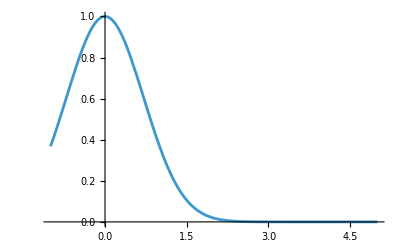

```mathematica
Plot[f6[a],{a, -1, 5}]
```

```mathematica
(* Problem 6 *)
```

```mathematica
f81[x_]:=Sin[x^2]
```

```mathematica
f82[x_]:= Cos[x^2]
```

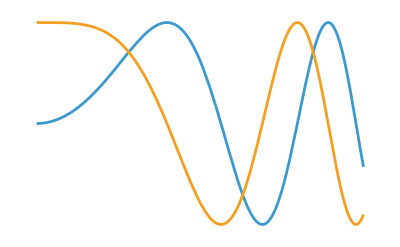

```mathematica
Plot[{f81[x],f82[x]},{x,0,Pi},Axes->False]
```

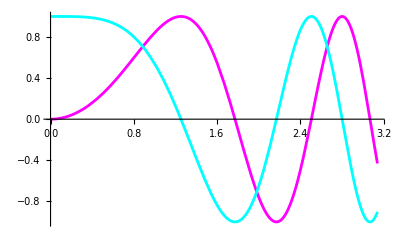

```mathematica
Plot[{f81[x],f82[x]},{x,0,Pi},PlotStyle->{Magenta,Cyan},Axes->True]
```

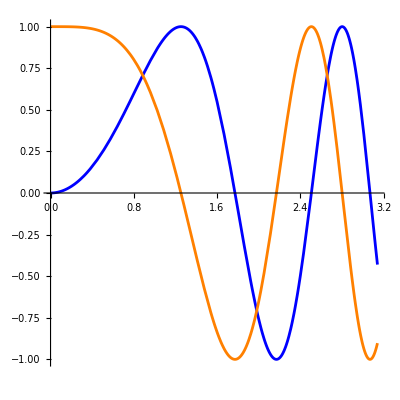

```mathematica
Plot[{f81[x],f82[x]},{x,0,Pi},PlotStyle->{Blue,Orange},Axes->True, AspectRatio->1]
```

```mathematica
(* Problem 7 *)
```

```mathematica
p71[x_]:=Sin[x]
```

```mathematica
p72[x_]:=Cos[x]
```

```mathematica
p73[x_]:=1/(x+1)
```

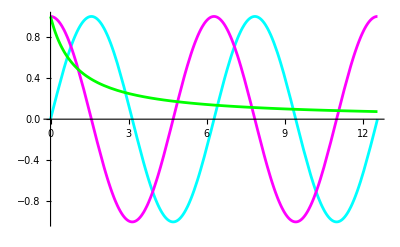

```mathematica
P7 = Plot[{p71[x],p72[x],p73[x]},{x,0,4*Pi},PlotStyle->{Cyan, Magenta, Green}]
```

```mathematica
(* Problem 8 *)
```

```mathematica
x8[t_]:=Cos[7*t]Cos[11*t]
```

```mathematica
y8[t_]:=Cos[7*t]Sin[11*t]
```

```mathematica
p8[t_]:={x8[t],y8[t]}
```

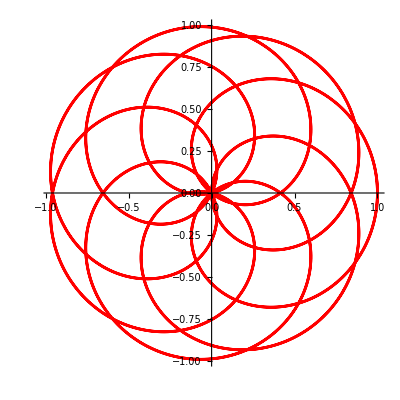

```mathematica
P8 = ParametricPlot[p8[t],{t,0,2Pi},PlotStyle->Red,AspectRatio->1]
```

```mathematica
(* Problem 9 *)
```

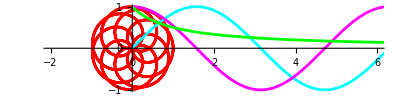

```mathematica
Show[{P8, P7}, PlotRange->{{-2,6},{-1,1}}, AspectRatio->1/4]
```

```mathematica
(* Problem 10 *)
```

```mathematica
x101[t_]:=Sin[t]
```

```mathematica
y101[t_]:=Cos[t^4]
```

```mathematica
x102[t_]:=Sin[t^2]
```

```mathematica
y102[t_]:=Cos[11*t]+Sqrt[t]
```

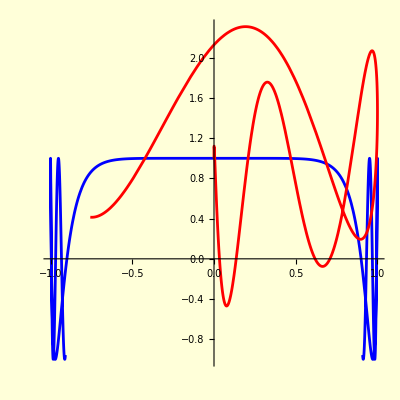

```mathematica
ParametricPlot[{{x101[t],y101[t]},{x102[t],y102[t]}},{t,-2,2},PlotStyle->{Blue,Red},Background->LightYellow, AspectRatio->1]
```

```mathematica
(* Primitives *)
```

```mathematica
(* Example-Array, Create an array 1,3,5,7,...,15 *)
```

```mathematica
fa[i_]:=2i-1
```

```mathematica
A1=Table[fa[i],{i,8}]
```

{1,3,5,7,9,11,13,15}

```mathematica
(* Example-Map, Create and plot and array fp[1], fp[3],..., fp[15] where fp[x_]:=Sin[x].*)
```

```mathematica
fp[x_]:=Sin[x]
```

```mathematica
SA1 = Table[1.0fp[A1[[i]]],{i,8}]
```

{0.841471,0.14112,-0.958924,0.656987,0.412118,-0.99999,0.420167,0.650288}

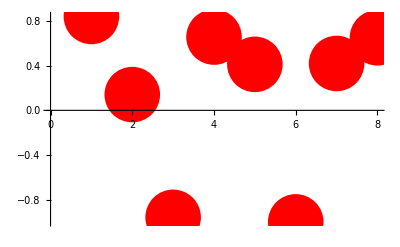

```mathematica
ListPlot[SA1,PlotStyle->{Red, PointSize[0.1]}]
```

```mathematica
(* Example-Create an array of points *)
```

```mathematica
GSA1 = Table[{i,SA1[[i]]},{i,8}]
```

{{1,0.841471},{2,0.14112},{3,-0.958924},{4,0.656987},{5,0.412118},{6,-0.99999},{7,0.420167},{8,0.650288}}

```mathematica
PSA1=Point[GSA1]
```

Point[{{1,0.841471},{2,0.14112},{3,-0.958924},{4,0.656987},{5,0.412118},{6,-0.99999},{7,0.420167},{8,0.650288}}]

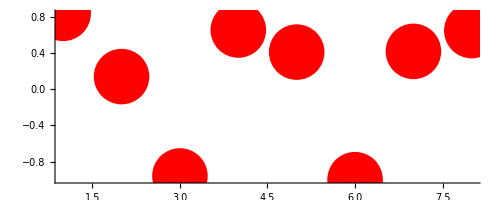

```mathematica
Graphics[{Red,PointSize[0.1],PSA1},Axes->True]
```

```mathematica
(* Problem 10 *)
```

```mathematica
C10=Circle[{0,0},5];
```

```mathematica
D10={Red,Disk[{2,2},3]};
```

```mathematica
P10={Blue,PointSize[0.03],Point[{3,3}]};
```

```mathematica
L10={Purple,Thick,Line[{{0,0},{3,3}}]};
```

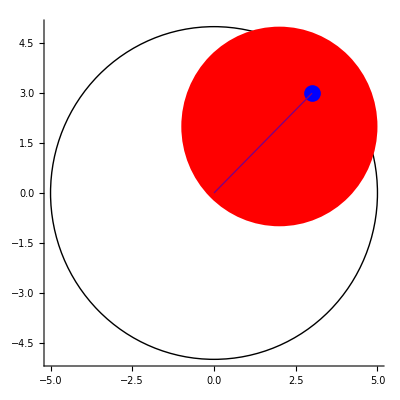

```mathematica
Graphics[{C10,D10,P10,L10},Axes->True]
```

```mathematica
(* Problem 11 *)
```

```mathematica
Clear[f]
```

```mathematica
f[x_]:={0.5-Random[], 0.5-Random[]}
```

```mathematica
Lrandom=Table[f[i],{i,15}]
```

{{0.0954099,-0.254861},{0.305962,0.0173239},{-0.0420814,-0.198341},{-0.300346,0.401215},{-0.310249,0.492585},{-0.30665,0.457014},{-0.118704,0.121916},{0.437543,-0.225415},{0.295615,0.307093},{0.453584,-0.454322},{-0.103765,-0.472834},{0.0302102,0.0130424},{0.300825,0.282027},{0.224248,0.495719},{-0.157094,-0.0196323}}

```mathematica
(* Show as a matrix *)
```

```mathematica
MatrixForm[Lrandom]
```

(0.0954099 | -0.254861
0.305962 | 0.0173239
-0.0420814 | -0.198341
-0.300346 | 0.401215
-0.310249 | 0.492585
-0.30665 | 0.457014
-0.118704 | 0.121916
0.437543 | -0.225415
0.295615 | 0.307093
0.453584 | -0.454322
-0.103765 | -0.472834
0.0302102 | 0.0130424
0.300825 | 0.282027
0.224248 | 0.495719
-0.157094 | -0.0196323)

```mathematica
(* Problem 12 *)
```

```mathematica
fPoint[P_]:=Point[P,VertexColors->RandomColor[]]
```

```mathematica
GPoints15=Table[fPoint[Lrandom[[i]]],{i,15}]
```

{Point[{0.0954099,-0.254861},VertexColors→RGBColor[0.20355608972391526, 0.015597340042968977, 0.4046617809774413]],Point[{0.305962,0.0173239},VertexColors→RGBColor[0.4311591534490027, 0.08925700820051263, 0.3924159588640659]],Point[{-0.0420814,-0.198341},VertexColors→RGBColor[0.49582728411137755, 0.2220050166896821, 0.6280570954401112]],Point[{-0.300346,0.401215},VertexColors→RGBColor[0.3677743529977573, 0.7684310122531566, 0.01714711024726867]],Point[{-0.310249,0.492585},VertexColors→RGBColor[0.7626478611717737, 0.14632895272507285, 0.00679674355618598]],Point[{-0.30665,0.457014},VertexColors→RGBColor[0.7844250570575468, 0.8749217825475593, 0.8366163127390511]],Point[{-0.118704,0.121916},VertexColors→RGBColor[0.3128791162290452, 0.4829654461280517, 0.7135520250678298]],Point[{0.437543,-0.225415},VertexColors→RGBColor[0.9550241450162773, 0.8914467115965745, 0.47520150723443755]],Point[{0.295615,0.307093},VertexColors→RGBColor[0.38658326082898564, 0.8534341789811659, 0.6040806330116979]],Point[{0.453584,-0.454322},VertexColors→RGBColor[0.49048848332100303, 0.7383558923927642, 0.24382031423752393]],Point[{-0.103765,-0.472834},VertexColors→RGBColor[0.5135812961924542, 0.5262310090586193, 0.6538902818483316]],Point[{0.0302102,0.0130424},VertexColors→RGBColor[0.7325464498520817, 0.270868893766506, 0.11992133531056504]],Point[{0.300825,0.282027},VertexColors→RGBColor[0.4573408849999885, 0.4891754656455787, 0.2749001894432148]],Point[{0.224248,0.495719},VertexColors→RGBColor[0.8232875202570078, 0.7165714080208399, 0.10947624068571282]],Point[{-0.157094,-0.0196323},VertexColors→RGBColor[0.5796415662932539, 0.8289571387998014, 0.9504895949331496]]}

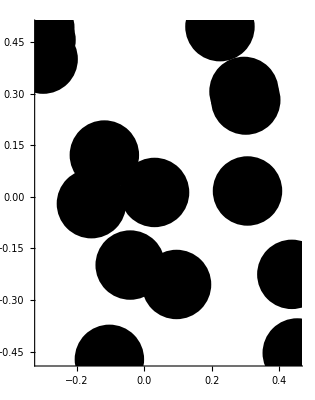

```mathematica
Graphics[{PointSize[0.15],GPoints15},Axes->True]
```

```mathematica
(* Problem 13 *)
```

```mathematica
fCircle[P_]:={RandomColor[], Circle[P,0.1]}
```

```mathematica
Circle15 =Table[fCircle[Lrandom[[i]]],{i,15}]
```

{{RGBColor[0.820243848518142, 0.7195663834003392, 0.2737577753034044],Circle[{0.0954099,-0.254861},0.1]},{RGBColor[0.20469000748529864, 0.1373491088924359, 0.2719828775804807],Circle[{0.305962,0.0173239},0.1]},{RGBColor[0.11236598025051947, 0.41430195105080836, 0.931512289679582],Circle[{-0.0420814,-0.198341},0.1]},{RGBColor[0.5095238791311223, 0.18461620618780517, 0.13237077065505165],Circle[{-0.300346,0.401215},0.1]},{RGBColor[0.1988321972726561, 0.12353796563401698, 0.9372347035223096],Circle[{-0.310249,0.492585},0.1]},{RGBColor[0.5204722944015445, 0.5787898970894065, 0.34499094154139454],Circle[{-0.30665,0.457014},0.1]},{RGBColor[0.6353904172935989, 0.18374776294514383, 0.19320326701770907],Circle[{-0.118704,0.121916},0.1]},{RGBColor[0.8949308031352932, 0.6455053765471457, 0.6061913627186719],Circle[{0.437543,-0.225415},0.1]},{RGBColor[0.3923700744556835, 0.20289540337110767, 0.03105887882841496],Circle[{0.295615,0.307093},0.1]},{RGBColor[0.7340630892701705, 0.3304422566470384, 0.739291465439164],Circle[{0.453584,-0.454322},0.1]},{RGBColor[0.7873078412163528, 0.050203368783463764, 0.4159034490649616],Circle[{-0.103765,-0.472834},0.1]},{RGBColor[0.6589504882671906, 0.527187455024869, 0.40268938020813594],Circle[{0.0302102,0.0130424},0.1]},{RGBColor[0.6174872950068144, 0.668946704107271, 0.34697490232432093],Circle[{0.300825,0.282027},0.1]},{RGBColor[0.1792790416853458, 0.980828662503463, 0.7407931150631746],Circle[{0.224248,0.495719},0.1]},{RGBColor[0.41781942545367556, 0.9132065604063919, 0.4563622552459554],Circle[{-0.157094,-0.0196323},0.1]}}

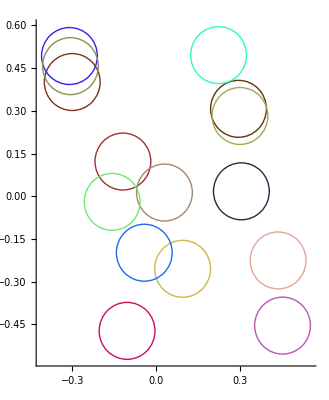

```mathematica
Graphics[Circle15,Axes->True]
```

```mathematica
(* Connect the points by lines *)
```

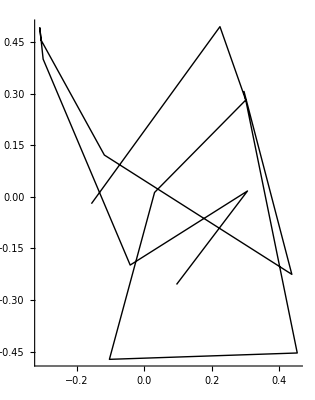

```mathematica
GLines15B = Graphics[Line[Lrandom],Axes->True]
```

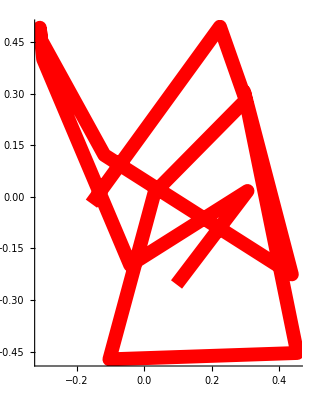

```mathematica
GLines15R=Graphics[{Red,Thickness[0.025],Line[Lrandom]},Axes->True]
```

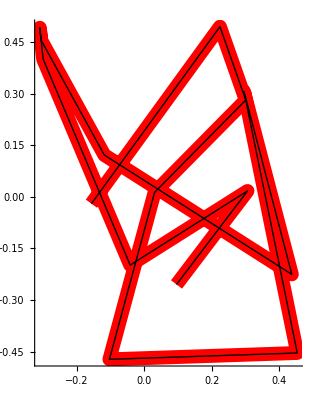

```mathematica
Show[GLines15R,GLines15B]
```

```mathematica
(* Bonus 1 Extra 1 Lab Point *)
```

```mathematica
fBonus1[P_]:={{RandomColor[], Disk[Lrandom[[i]],0.1]},{RandomColor[], Disk[Lrandom[[i]],0.05]}}
```

```mathematica
B1 =Table[fBonus1[Lrandom[[i]]],{i,15}]
```

{{{RGBColor[0.11310212183333102, 0.8287926254336828, 0.5842565564085405],Disk[{0.0954099,-0.254861},0.1]},{RGBColor[0.8501016298129969, 0.9831524177488169, 0.24611647136053727],Disk[{0.0954099,-0.254861},0.05]}},{{RGBColor[0.8844687855791702, 0.9038620154269299, 0.8979350815280236],Disk[{0.305962,0.0173239},0.1]},{RGBColor[0.44844982879214923, 0.13879528688595166, 0.6264228783847992],Disk[{0.305962,0.0173239},0.05]}},{{RGBColor[0.7274858166914324, 0.7569642003726338, 0.7260404090181845],Disk[{-0.0420814,-0.198341},0.1]},{RGBColor[0.09928588757926704, 0.48348300343844697, 0.39085431077357735],Disk[{-0.0420814,-0.198341},0.05]}},{{RGBColor[0.6083937422593559, 0.38164783646797695, 0.9625145912992039],Disk[{-0.300346,0.401215},0.1]},{RGBColor[0.7374578355114119, 0.05936161096139059, 0.6992096133004277],Disk[{-0.300346,0.401215},0.05]}},{{RGBColor[0.5303601913318818, 0.3662749974640782, 0.789251147022588],Disk[{-0.310249,0.492585},0.1]},{RGBColor[0.44015232566449125, 0.3726218882485721, 0.9448781292970578],Disk[{-0.310249,0.492585},0.05]}},{{RGBColor[0.28602800924425975, 0.7077219481694597, 0.9842699835755506],Disk[{-0.30665,0.457014},0.1]},{RGBColor[0.1610082035125413, 0.601473834664715, 0.07345230871313557],Disk[{-0.30665,0.457014},0.05]}},{{RGBColor[0.7316098057075056, 0.17968559133223438, 0.7553890516524522],Disk[{-0.118704,0.121916},0.1]},{RGBColor[0.6620676513487509, 0.9065339209825185, 0.8883007638211393],Disk[{-0.118704,0.121916},0.05]}},{{RGBColor[0.1976259329074912, 0.35207493360542985, 0.030905173136297037],Disk[{0.437543,-0.225415},0.1]},{RGBColor[0.00048165778749309496, 0.11340450899233923, 0.8880692843100446],Disk[{0.437543,-0.225415},0.05]}},{{RGBColor[0.8920978347654327, 0.48484547117213816, 0.9185277083152574],Disk[{0.295615,0.307093},0.1]},{RGBColor[0.6999168712218165, 0.0842886677720085, 0.16438654069198355],Disk[{0.295615,0.307093},0.05]}},{{RGBColor[0.5823822607027733, 0.8766606687477796, 0.4480140290789454],Disk[{0.453584,-0.454322},0.1]},{RGBColor[0.21713487546492183, 0.3297671317490767, 0.7574901940644903],Disk[{0.453584,-0.454322},0.05]}},{{RGBColor[0.2029863505122893, 0.9151531185183923, 0.6812027461313765],Disk[{-0.103765,-0.472834},0.1]},{RGBColor[0.9667302580648873, 0.6966726121146152, 0.5768634282300247],Disk[{-0.103765,-0.472834},0.05]}},{{RGBColor[0.169367170601757, 0.6702039398923672, 0.5321550389254595],Disk[{0.0302102,0.0130424},0.1]},{RGBColor[0.5100284209733534, 0.5637025976316332, 0.9167847664801219],Disk[{0.0302102,0.0130424},0.05]}},{{RGBColor[0.30229905260952017, 0.5371300606247167, 0.026262268990160376],Disk[{0.300825,0.282027},0.1]},{RGBColor[0.2125607715809421, 0.1329088470656712, 0.251565963864518],Disk[{0.300825,0.282027},0.05]}},{{RGBColor[0.6634178783795444, 0.8379017264066102, 0.5497604674024132],Disk[{0.224248,0.495719},0.1]},{RGBColor[0.6019573553799491, 0.20889510513985265, 0.7276322137048319],Disk[{0.224248,0.495719},0.05]}},{{RGBColor[0.10532155599892001, 0.5290429500721043, 0.9274078831972026],Disk[{-0.157094,-0.0196323},0.1]},{RGBColor[0.4834925191110062, 0.024287177613973254, 0.28417265761537425],Disk[{-0.157094,-0.0196323},0.05]}}}

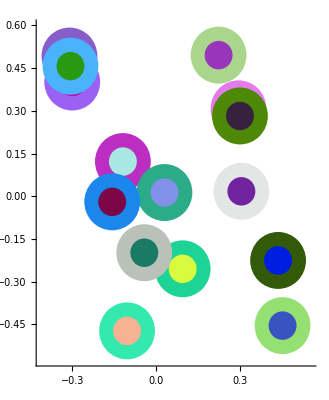

```mathematica
T1 = Graphics[{B1,PointSize[0.001]},Axes->True]
```

```mathematica
(* Bonus 2 *)
```

```mathematica
(* LRect15[P_]:={Line[{{0.1,1},{1.1,1},{1.1,0},{0.1,0},{0.1,1}}]} *)
```

```mathematica
LRect15[P_]:=Line[{{P-0.1,P+{-0.1,0.1},P+0.1,P+{0.1,-0.1},P-0.1}}]
```

```mathematica
LRect151 =Table[LRect15[Lrandom[[i]]],{i,15}]
```

{Line[{{{-0.00459011,-0.354861},{-0.00459011,-0.154861},{0.19541,-0.154861},{0.19541,-0.354861},{-0.00459011,-0.354861}}}],Line[{{{0.205962,-0.0826761},{0.205962,0.117324},{0.405962,0.117324},{0.405962,-0.0826761},{0.205962,-0.0826761}}}],Line[{{{-0.142081,-0.298341},{-0.142081,-0.0983408},{0.0579186,-0.0983408},{0.0579186,-0.298341},{-0.142081,-0.298341}}}],Line[{{{-0.400346,0.301215},{-0.400346,0.501215},{-0.200346,0.501215},{-0.200346,0.301215},{-0.400346,0.301215}}}],Line[{{{-0.410249,0.392585},{-0.410249,0.592585},{-0.210249,0.592585},{-0.210249,0.392585},{-0.410249,0.392585}}}],Line[{{{-0.40665,0.357014},{-0.40665,0.557014},{-0.20665,0.557014},{-0.20665,0.357014},{-0.40665,0.357014}}}],Line[{{{-0.218704,0.0219156},{-0.218704,0.221916},{-0.0187041,0.221916},{-0.0187041,0.0219156},{-0.218704,0.0219156}}}],Line[{{{0.337543,-0.325415},{0.337543,-0.125415},{0.537543,-0.125415},{0.537543,-0.325415},{0.337543,-0.325415}}}],Line[{{{0.195615,0.207093},{0.195615,0.407093},{0.395615,0.407093},{0.395615,0.207093},{0.195615,0.207093}}}],Line[{{{0.353584,-0.554322},{0.353584,-0.354322},{0.553584,-0.354322},{0.553584,-0.554322},{0.353584,-0.554322}}}],Line[{{{-0.203765,-0.572834},{-0.203765,-0.372834},{-0.0037652,-0.372834},{-0.0037652,-0.572834},{-0.203765,-0.572834}}}],Line[{{{-0.0697898,-0.0869576},{-0.0697898,0.113042},{0.13021,0.113042},{0.13021,-0.0869576},{-0.0697898,-0.0869576}}}],Line[{{{0.200825,0.182027},{0.200825,0.382027},{0.400825,0.382027},{0.400825,0.182027},{0.200825,0.182027}}}],Line[{{{0.124248,0.395719},{0.124248,0.595719},{0.324248,0.595719},{0.324248,0.395719},{0.124248,0.395719}}}],Line[{{{-0.257094,-0.119632},{-0.257094,0.0803677},{-0.0570937,0.0803677},{-0.0570937,-0.119632},{-0.257094,-0.119632}}}]}

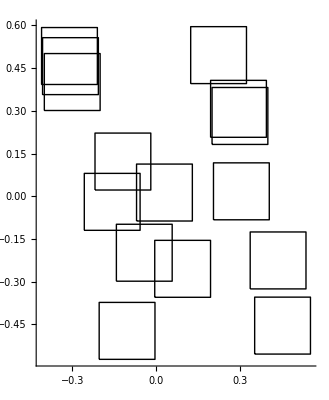

```mathematica
GRect15=Graphics[{LRect151},Axes->True]
```

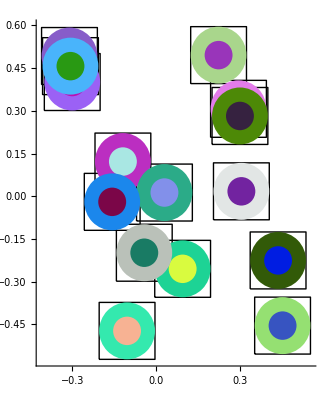

```mathematica
Show[GRect15,T1]
```